```mathematica
M=5.972*10^24; 
ρ=5515;
ω=1*10^-3;
α= 10^4;
β = 10^4;
c=3*10^8;
h=6.6*10^-34/2/Pi;
R=6371*10^3;
Q=7500;
u=7.6*10^-8;
p=10^-3*ω/(2 Pi c);
q=ω/α;
```

```mathematica
l=0
```

1.88496×10^15

0

```mathematica
D[SphericalBesselJ[0,z],z]/.{z->q r};
NIntegrate[Conjugate[%]*%r^2,{r,0,R}];
cn=Sqrt[M/(4Pi%*ρ)]
```

6.25727

```mathematica
D[SphericalBesselJ[0,z],z]/.{z->q r};
NIntegrate[%*SphericalBesselJ[1,p r]r^2,{r,0,R}]
f=Sqrt[3]M u/( Q(4Pi)cn%SphericalHarmonicY[1,0,0,0])
```

-1.20197×10^10

-226.981

```mathematica
l>0
```

False

```mathematica
Clear[lMode]
```

```mathematica
Quiet[intList={};
fList={};
For[lMode=0,lMode<10,lMode++,
lRange=5;
aAngularInt=Table[Integrate[SphericalHarmonicY[lMode,0,θ,ϕ]*Conjugate[SphericalHarmonicY[l,0,θ,ϕ]]*Cos[θ]*Sin[θ],{θ,0,Pi},{ϕ,0,2*Pi}],{l,0,lRange}];
bAngularInt=Table[Integrate[D[SphericalHarmonicY[lMode,0,θ,ϕ],θ]*Conjugate[SphericalHarmonicY[l,0,θ,ϕ]]*Sin[θ]*Sin[θ],{θ,0,Pi},{ϕ,0,2*Pi}],{l,0,lRange}];
p=10^-3*ω/(2 Pi c);
q=ω/α;
k=ω/β;
alpha=0.5*((D[D[SphericalBesselJ[lMode,z],z],z]/.{z->k R})+(lMode-1)(lMode+2)(SphericalBesselJ[lMode,z]/.{z->k R})/(k R)^2);
beta=N[q/k D[SphericalBesselJ[lMode,z]/z,z]/.{z->q R}];
a=alpha*(D[SphericalBesselJ[lMode,z],z]/.{z->q r})-beta*lMode*(lMode+1)SphericalBesselJ[lMode,k r]/(k r);
b=r/R(alpha*SphericalBesselJ[lMode,q r]/(q r)-beta (SphericalBesselJ[lMode,k r]/(k r)+D[SphericalBesselJ[lMode,z],z]/.{z->k r}));
cn=Sqrt[M/ρ /NIntegrate[(a^2*Conjugate[SphericalHarmonicY[lMode,0,θ,ϕ]]*SphericalHarmonicY[lMode,0,θ,ϕ]
+b^2 R^2 (1/r^2 Conjugate[D[SphericalHarmonicY[lMode,0,θ,ϕ],θ]]*D[SphericalHarmonicY[lMode,0,θ,ϕ],θ]+
1/r^2 /Sin[θ]^2Conjugate[D[SphericalHarmonicY[lMode,0,θ,ϕ],ϕ]]*D[SphericalHarmonicY[lMode,0,θ,ϕ],ϕ]))
r^2 Sin[θ],{r,0,R},{θ,0,Pi},{ϕ,0,2*Pi}]];
int=NIntegrate[(aAngularInt*a*Table[I^lBes SphericalHarmonicY[lBes,0,0,0] SphericalBesselJ[lBes,p r],{lBes,0,lRange}]+R*bAngularInt*b*Table[I^lBes SphericalHarmonicY[lBes,0,0,0]SphericalBesselJ[lBes,p r],{lBes,0,lRange}])r^2,{r,0,R}];
fList=Append[fList,Abs[u M/(Q 4Pi cn Total[int])]];
intList=Append[intList,Abs[Total[int]]];
]]
intList
fList
```

{8.29776×10^9,8.5251×10^23,4.51241×10^13,425.7,1.4289×10^-9,2.26884×10^-21,1.99614×10^-33,0.,0.,0.}

{64.0302,1.94246×10^-14,0.000011659,18292.,3.88224×10^13,1.04423×10^23,3.4134×10^32,∞,∞,∞}

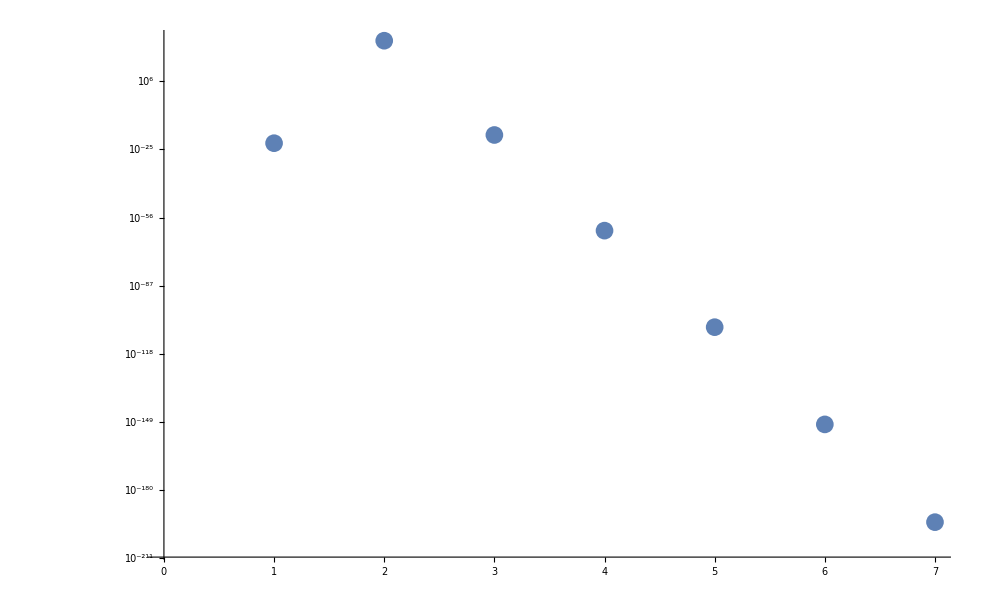

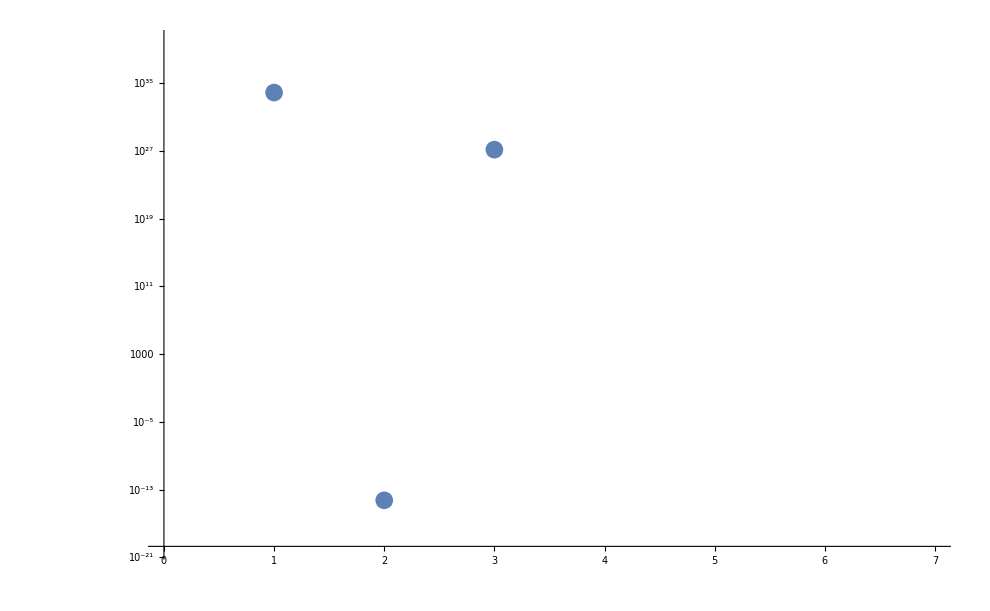

```mathematica
ListLogPlot[Abs[intList]]
ListLogPlot[Abs[fList]]
```